```mathematica
Format[FonzForm[x_]]:=x/.fonz->-Graphics-
Format[Unique[],FonzForm]:=Null
```

```mathematica
a+fonz//FonzForm
```

a+-Graphics-

```mathematica
Clear[σ,x]
σ[z_]:=1/(1+ⅇ^-z)
Dt[σ[x],x]
Simplify[Dt[σ[x],x]==σ[x](1-σ[x])]
```

ⅇ^-x/((1+ⅇ^-x)^2)

True

```mathematica
Clear[σ]
σ'[z_]:=σ[z](1-σ[z])
Dt[σ[x],x]
σ'[z]
Unevaluated[Derivative[1][σ][y]]//FullForm
SubValues[Derivative]
```

(1-σ[x]) σ[x]

(1-σ[z]) σ[z]

Unevaluated[Derivative[1][\[Sigma]][y]]

{HoldPattern[σ'[z_]]:>σ[z] (1-σ[z])}

```mathematica
Clear[f,g,x]
x=1;
f[x_]:=1
g[h[x_]]^:=gh[x]
a[1][b]:=c
N[g[x_]]:=x+1
g[1]
N[g[1]]

OwnValues[x]
DownValues[f]
DownValues[g]
UpValues[h]
SubValues[a]
NValues[g]
```

g[1]

2.

{HoldPattern[x]:>1}

{HoldPattern[f[x_]]:>1}

{}

{HoldPattern[g[h[x_]]]:>gh[x]}

{HoldPattern[a[1][b]]:>c}

{HoldPattern[N[g[x_],{MachinePrecision,MachinePrecision}]]:>x+1}

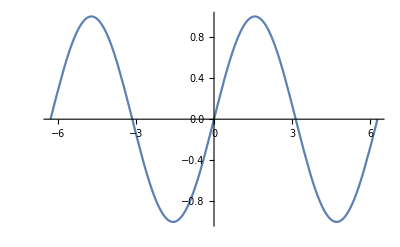

```mathematica
Plot[Sin[x],{x,-2π,2π},Method->{Compiled->False}]
```